# Data analysis of the dynamics of states in the GP equation

```mathematica
(*Importing data from julia*)
SetDirectory[NotebookDirectory[]];
datawf=Import["output/wavefunction.dat"];
datawigner=Import["output/wignerfunction.dat"];
datasa=Import["output/survivalamplitude.dat"];
```

#### Classical trajectories

```mathematica
(*Classical Hamiltonian*)
a=-5;
b=1;
mp=5;
H[q_,p_,t_]=p^2/(2*mp) +a*q^2+b*q^4;
```

```mathematica
(*Solving the Hamiltons equation*)
pin=0.01;
qin=0;
tf=20000;
T=0.1;
sol=NDSolve[{D[q[t],t]==D[H[q[t],p[t],t],p[t]],D[p[t],t]==-D[H[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
```

```mathematica
(*Classical trajectories and Poncaire sections*)
qp=Table[{q[t],p[t]}/.sol[[1]]/.t->i,{i,0,tf,T}];
```

```mathematica
sep=ListPlot[{qp},PlotStyle->Darker[Green],Frame->True]
```

-Graphics-

#### Wigner function

```mathematica
NN=500;(*Number of subintervals in the grid (must coincide the N in the Julia code)*)
L=2*20;(* Size of the space (must coincide the N in the Julia code)*)
Wvol=Sum[(L/NN)*(L/NN)*datawigner[[i,3]],{i,1,Length[datawigner]}](*Volume of the Wigner function*)
Wneg=Sum[(L/NN)*(L/NN)*Abs[datawigner[[i,3]]],{i,1,Length[datawigner]}]-Wvol(*Wigner negativity*)
```

0.991797

2.22045×10^-16

```mathematica
(*Color for the Wigner function*)
FCo[t_]=Piecewise[{{ RGBColor[1,(2t)^3,(2t)^3],0<=t<=1/2},{ RGBColor[(1-2(t-1/2)),(1-2(t-1/2)),1],1/2<t<=1}}];
```

```mathematica
(*Wigner function and Poncaire sections*)wigner2=Show[ListDensityPlot[datawigner,PlotRange->{{-8,8},{-8,8},All},Frame->  True,LabelStyle->Directive[Bold,Medium],ColorFunction->(FCo[1-0.5/0.35 (#+0.35)]&),ColorFunctionScaling->False,PlotLegends->Automatic],sep]
```

-Graphics-

#### Probability Density

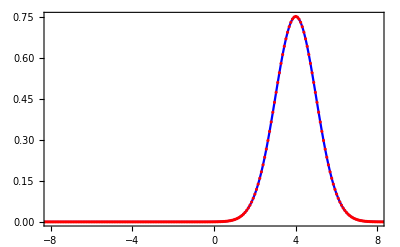

```mathematica
(*Probability density*)
datawfn=Table[{datawf[[i,1]],Abs[datawf[[i,2]]+I*datawf[[i,3]]]},{i,1,Length[datawf]}];
ListPlot[{datawfn,datawfn},PlotRange->{{-8,8},All},Joined->{True,False},Frame->True,LabelStyle->{Black,15},PlotStyle->{Blue,Red}]
```

#### Survival amplitude

```mathematica
mp=5;(*Physical mass*)
ampcomp=Table[datasa[[i,2]]+I*datasa[[i,3]],{i,1,Length[datasa]}];
ratefunction=Table[{datasa[[i,1]],-(1/mp)*Log[Abs[ampcomp[[i]]]^2]},{i,1,Length[ampcomp]}];
```

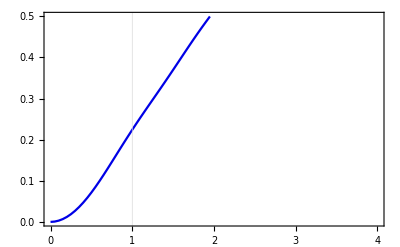

```mathematica
figsa=ListPlot[{ratefunction},PlotRange->{{0,4},All},PlotStyle->{Darker[Blue,0.1],{Darker[Green,0.1],Dashed},{Darker[Red,0.1],Dashed}},PlotLegends->{},Frame->True,Joined->True,LabelStyle->{18,Black},FrameLabel->{},GridLines->{{1},{}},GridLinesStyle->{{Dashed,Red,Thickness[0.007]},{Thick,Red,Dashed}}]
```